# ON THE SIGN CHANGES OF ψ(x)−x

## Heuristic computations accompanying the paper

M. Grześkowiak, J. Kaczorowski, Ł. Pańkowski, M. Radziejewski

This notebook documents how we searched for contour parameters to be used in the rigorous proof. Wherever possible, we use the notation from the paper, section “The proof of Theorem 1”. Some peculiarities of the code below result from how Mathematica is designed:

Wherever we need a variable with a capitalized name, we precede it with lowercase “c”, for “capital”, because names starting with a capital letter are reserved for Mathematica symbols.

Numerical constants (e.g., those used in defining the contour) are entered using Mathematica’s backtick notation, like 0.025`100. This tells Mathematica that it is ok to perform high-precision calculations on this number. An exact decimal that we meant, 0.025, would be interpreted as a machine-precision number, a notion which would propagate to all derived quantities and cause any high-precision settings to be disregarded. This is not always desirable.

This notebook is also available as a PDF file for viewing without Mathematica.

## Initialization

```mathematica
cN=21; (* The main parameter, N in the paper. *)
epsilon=3.32`100×10^-13; (* Obtained from Algorithm 1 for the given N. *)
precision = 100; (* The precision to be used in most of our calculations. *)
numZeros=10000; (* Zeros to be used in estimating R_N(y), denoted N' in the paper. *)
$MaxExtraPrecision=2*precision;
Parallelize[imZero=Table[N[Im[ZetaZero[k]],{Infinity,precision+10}],{k,1,numZeros}]];
gamma[n_]:=imZero[[n+1]]; (* Conversion between our 0-based indexing and Mathematica's 1-based arrays. *)
rho[n_]:=1/2+I gamma[n]; (* Conversion between our 0-based indexing and Mathematica's 1-based arrays. *)
omega[n_] := gamma[n]-gamma[0];
cNPrime=numZeros-2;
error=10^(5-precision);  (* For basic upward rounding. *)
aUpperBound[n_]:=(Abs[rho[0]]+error)/(Abs[rho[n]]-error) (* Upper bound for |a(n)|. *)
cT1=(gamma[cNPrime]+gamma[cNPrime+1])/2;
(* The upper bound for R_N(y). *)
cRNprec[y_]:=Sum[aUpperBound[n] Exp[y(error-omega[n])],{n,cN+1,cNPrime}]+
((Abs[rho[0]]+error)Exp[y(gamma[0]-cT1+error)]/(cT1-error))(Log[cT1+error](4+1/(2 Pi y))+2/(y(cT1-error)));
(* The upper bound for R_N is slightly expensive to compute, so we are going to pre-compute it at 0.00001, 0.00002, ..., 0.15. *)
cRNprecTop=0.15`100;
cRNprecRes=15000;
Parallelize[cRNprecArray=Table[cRNprec[cRNprecTop*j/cRNprecRes],{j,1,cRNprecRes}]];
cRNest[y_]:=Module[{t,j},
t=cRNprecRes*y/cRNprecTop;
j=Floor[t];
t-=j;
If[j>=cRNprecRes,cRNprecArray[[j]],
cRNprecArray[[j]](1-t)+cRNprecArray[[j+1]]t]
];
norm[x_]:=Abs[x-Round[x]];
cFNEta[z_]:=1-Sum[(Abs[rho[0]]/Abs[rho[n]])Exp[omega[n]*z*I],{n,1,cN}];
f[z_]:=-Sum[I*omega[n]*(Abs[rho[0]]/Abs[rho[n]])Exp[omega[n]*z*I],{n,1,cN}];

(* The function below gives a non-rigorous estimate of the final result,
meant for finding contour parameters using fewer contour points. *)
resultApproximate[(* contour position *) paramdelta_?NumericQ,paramcontourTop_?NumericQ,paramcontourBottom_?NumericQ,(* a function that goes from the value 0 at 0 to the value π at 4, that determines α_j`s in the paper *) argFun_,
(* m/8, i.e. half of the number of divisions of the contour on each side *) contourRes_?NumericQ,
(* l, i.e. the resolution for approximating weight functions *) weightRes_?IntegerQ
]:=
Module[
{
delta,contourTop,contourBottom,
m,t,z1,cRNArray,alpha,
b,xPrime,xBis,y,
indexForRN,M,u,
betaPrime,betaBis,phiPrime,phiBis,c,symmetricPairs,phi,c0j,cn0,
operation,wnInverse,wnMax,wnScale,localc,localphi,cosphi,iMax,cosValue,previous,product,volume,returnValue,
epsmachine,
i,j,n
},
delta=SetPrecision[paramdelta,precision];
contourTop=SetPrecision[paramcontourTop,precision];
contourBottom=SetPrecision[paramcontourBottom,precision];
m=8*contourRes;
t[j_]:=j/m;
(*z1(t_j) is to be stored as z1[[j+1]].*)
z1=Join[Table[(-0.5`100+j/(2*contourRes))*delta+contourBottom*I,{j,0,2*contourRes}],Table[0.5`100*delta+(contourBottom+(contourTop-contourBottom)*j/(2*contourRes))*I,{j,1,2*contourRes}],Table[(0.5`100-j/(2*contourRes))*delta+contourTop*I,{j,1,2*contourRes}],Table[-0.5`100*delta+(contourTop-(contourTop-contourBottom)*j/(2*contourRes))*I,{j,1,2*contourRes}]];
alpha=Join[Table[-Pi-argFun[1-(j-1)/contourRes],{j,1,contourRes}],
Table[-Pi+argFun[(j-1)/contourRes],{j,1,4*contourRes}],
Table[Pi-argFun[4-(j-1)/contourRes],{j,1,3*contourRes+1}]];

(*Claim 1.*)
(*Subsequent alpha[[j]] should differ by less than π.*)
If[Max[Table[Abs[alpha[[j+1]]-alpha[[j]]],{j,1,m}]]>Pi-error,Return[-1.1]];
(*This value should be less than π.*)
If[Max[Table[Abs[z1[[j+1]]-z1[[j]]],{j,1,m}]]*omega[cN]>Pi-error,Return[-1.2]];

xPrime=Table[Re[z1[[j]]],{j,1,m}];
y=Table[Im[z1[[j]]],{j,1,m}];
cRNArray=Table[cRNest[y[[j]]],{j,1,m}];
u=Table[Re[cFNEta[z1[[j]]] Exp[-I*alpha[[j]]]]-cRNArray[[j]],{j,1,m}];

(*Claim 2.*)
(*This value should be positive.*)
If[Min[u]<error,Return[-2]];

betaPrime=Table[Table[Pi+omega[n]*xPrime[[j]]-alpha[[j]],{j,1,m}],{n,1,cN}];
phiPrime=Table[Table[2*Pi*norm[betaPrime[[n]][[j]]/(2*Pi)],{j,1,m}],{n,1,cN}];
c=Table[Table[(aUpperBound[n]/u[[j]])*Exp[-omega[n]*y[[j]]],{j,1,m}],{n,1,cN}];
(*Because of the symmetry cFNEta[-x+y I]==cFNEta[x+y I] we can skip half of the intervals.This part does not appear in the paper as it is just a numerical optimization.We do not include it in the rigorous check.This allows us to shorten the iterative process of choosing best division points.*)
(*We leave out the repeated entries.*)
For[n=1,n<=cN,n++,
c[[n]]=c[[n]][[contourRes+1;;5*contourRes]];
phiPrime[[n]]=phiPrime[[n]][[contourRes+1;;5*contourRes]];
];
u=u[[contourRes+1;;5*contourRes]];
y=y[[contourRes+1;;5*contourRes]];
phi=phiPrime;
wnMax=Table[Min[1,Max[Table[(c[[n]][[j]]+error)*(Cos[phi[[n]][[j]]]+1),{j,Length[c[[n]]]}]]],{n,cN}];
For[n=cN-1,n>=1,n--,wnMax[[n]]+=wnMax[[n+1]]];
wnScale=Table[1,{n,cN}];
For[n=2,n<=cN-1,n++,wnScale[[n]]=Max[1,Floor[(1/2-error)/(wnScale[[n-1]]*wnMax[[n]])]]*wnScale[[n-1]]];
wnScale[[cN]]=wnScale[[cN-1]];
For[n=cN,n>=1,n--,
operation="Computing";
epsmachine=0.0+epsilon;
wnInverse=Table[0.5,{i,weightRes}];
For[j=1,j<=Length[c[[n]]],j++,
localc=0.0+wnScale[[n]]*(c[[n]][[j]]+error);(*To machine precision*)
localphi=0.0+phi[[n]][[j]];
cosphi=Cos[localphi];
iMax=Floor[Min[1,localc*(cosphi+1)]*weightRes];
For[i=1,i<=iMax,i++,
(*Solve c(Cos[ϕ]-Cos[ϕ+2π(epsilon+x)])==i/weightRes*)
cosValue=cosphi-i/(weightRes*localc);
wnInverse[[i]]=Min[wnInverse[[i]],(ArcCos[cosValue]-localphi)/(2 Pi)-epsmachine]
];
];
For[i=weightRes,i>=1,i--,
wnInverse[[i]]=Floor[wnInverse[[i]]*weightRes^2]
];
For[i=weightRes,i>=2,i--,
wnInverse[[i]]-=wnInverse[[i-1]]
];
If[n==cN,
previous=wnInverse
,
operation="Convoluting";
If[wnScale[[n]]<wnScale[[n+1]],
For[i=1,i<=Floor[weightRes*wnScale[[n]]/wnScale[[n+1]]],i++,
previous[[i]]=Sum[previous[[j]],{j,1+(wnScale[[n+1]]/wnScale[[n]])*(i-1),(wnScale[[n+1]]/wnScale[[n]])*i}]
];
For[i=1+Floor[weightRes*wnScale[[n]]/wnScale[[n+1]]],i<=weightRes,i++,
previous[[i]]=0
]
];
product=Join[{0},ListConvolve[previous,wnInverse,1,0][[1;;weightRes-1]]];
previous=product
]
];
volume=2^cN*Sum[product[[i]],{i,weightRes}]/weightRes^(2 cN);
returnValue=2*volume/delta;
returnValue
];
listplot[t_,label_:""]:=ListPlot[t,ImageSize->Large,GridLines->Automatic,PlotRange->Full,PlotLabel->label];

(*Simple 1D optimization, suitable for functions that take minutes to evaluate at a single point.*)
findMax[function_,x1_,x2_,iter_]:=
Module[{args,vals,i,j,go},
go[num_]:=Module[{},
vals[[num]]=function[args[[num]]]
];
args={0,0,0,0,0};
vals={0,0,0,0,0};
i=0;
For[j=1,j<=5,j++,
args[[j]]=x1+(j-1)*(x2-x1)/4
];
For[j=1,j<=5,j++,
go[j]
];
For[i=0,i<iter,,
j=Ordering[vals,-1][[1]];
If [j>=2&&j<=4,
i+=1;
args={args[[j-1]],(args[[j-1]]+args[[j]])/2,args[[j]],(args[[j]]+args[[j+1]])/2,args[[j+1]]};
vals={vals[[j-1]],0,vals[[j]],0,vals[[j+1]]};
If[vals[[1]]>=vals[[5]],
go[2];
If[vals[[2]]<=vals[[3]],go[4]]
,
go[4];
If[vals[[4]]<=vals[[3]],go[2]]
]
,
i-=1;
If[j==1,
args={2*args[[1]]-args[[5]],2*args[[1]]-args[[3]],args[[1]],args[[3]],args[[5]]};
vals={0,0,vals[[1]],vals[[3]],vals[[5]]};
go[2];
If[vals[[2]]>=vals[[3]],go[1]]
,
args={args[[1]],args[[3]],args[[5]],2*args[[5]]-args[[3]],2*args[[5]]-args[[1]]};
vals={vals[[1]],vals[[3]],vals[[5]],0,0};
go[4];
If[vals[[4]]>=vals[[3]],go[5]]
]
];
];
j=Ordering[vals,-1][[1]];
{args[[j]],vals[[j]]}
];
```

## Finding a good set of parameters

For a given delta we try to find a satisfactory argument function of a very simple form, then find a good value of contour bottom (), then the argument function and  again.
We also try an alternative approach, namely to do the same in reverse order.

```mathematica
parameters1[delta_]:=Module[
{aFixed=1.8,y0Fixed=0.0468,cRes=1000,wRes=4000},
aFixed=findMax[Function[a,resultApproximate[delta,0.14,y0Fixed,Interpolation[{{0,0},{1,a},{3,N[Pi,precision]},{4,N[Pi,precision]}},InterpolationOrder->1],cRes,wRes]],aFixed-0.2,aFixed+0.2,10][[1]];
y0Fixed=findMax[Function[y0,resultApproximate[delta,0.14,y0,Interpolation[{{0,0},{1,aFixed},{3,N[Pi,precision]},{4,N[Pi,precision]}},InterpolationOrder->1],cRes,wRes]],y0Fixed-0.00016,y0Fixed+0.00016,8][[1]];
aFixed=findMax[Function[a,resultApproximate[delta,0.14,y0Fixed,Interpolation[{{0,0},{1,a},{3,N[Pi,precision]},{4,N[Pi,precision]}},InterpolationOrder->1],cRes,wRes]],aFixed-0.2,aFixed+0.2,10][[1]];
y0Fixed=findMax[Function[y0,resultApproximate[delta,0.14,y0,Interpolation[{{0,0},{1,aFixed},{3,N[Pi,precision]},{4,N[Pi,precision]}},InterpolationOrder->1],cRes,wRes]],y0Fixed-0.00016,y0Fixed+0.00016,8][[1]];
{y0Fixed,aFixed}
];
parameters2[delta_]:=Module[
{aFixed=1.8,y0Fixed=0.0468,cRes=1000,wRes=4000},
y0Fixed=findMax[Function[y0,resultApproximate[delta,0.14,y0,Interpolation[{{0,0},{1,aFixed},{3,N[Pi,precision]},{4,N[Pi,precision]}},InterpolationOrder->1],cRes,wRes]],y0Fixed-0.00016,y0Fixed+0.00016,8][[1]];
aFixed=findMax[Function[a,resultApproximate[delta,0.14,y0Fixed,Interpolation[{{0,0},{1,a},{3,N[Pi,precision]},{4,N[Pi,precision]}},InterpolationOrder->1],cRes,wRes]],aFixed-0.2,aFixed+0.2,10][[1]];
y0Fixed=findMax[Function[y0,resultApproximate[delta,0.14,y0,Interpolation[{{0,0},{1,aFixed},{3,N[Pi,precision]},{4,N[Pi,precision]}},InterpolationOrder->1],cRes,wRes]],y0Fixed-0.00016,y0Fixed+0.00016,8][[1]];
aFixed=findMax[Function[a,resultApproximate[delta,0.14,y0Fixed,Interpolation[{{0,0},{1,a},{3,N[Pi,precision]},{4,N[Pi,precision]}},InterpolationOrder->1],cRes,wRes]],aFixed-0.2,aFixed+0.2,10][[1]];
{y0Fixed,aFixed}
];
```

The next part of the computation was performed on a remote machine and we only record the result here.

```mathematica
(*
Parallelize[fit=Table[
If[j<=8,
Join[{0.127+0.001*j},parameters1[0.127+0.001*j]],
Join[{0.127+0.001*(j-8)},parameters2[0.127+0.001*(j-8)]]
],{j,16}]];*)
fit={{0.128,0.046959062499999996,1.8543945312500005},{0.129,0.04695250000000001,1.8616210937500002},{0.13,0.04695250000000001,1.8689453124999997},{0.131,0.04695250000000001,1.876171875},{0.132,0.046891875,1.88369140625},{0.133,0.046891875,1.8909179687500002},{0.134,0.046891875,1.89775390625},{0.135,0.04689187500000001,1.90537109375},{0.128,0.046959062499999996,1.85439453125},{0.129,0.0469525,1.86162109375},{0.13,0.046893437499999996,1.869140625},{0.131,0.046891875,1.8763671875},{0.132,0.04689187500000001,1.88369140625},{0.133,0.04689187500000001,1.89091796875},{0.134,0.04689187500000001,1.8977539062499997},{0.135,0.046891875,1.90517578125}};
```

We check that the differences between parameters fitted in two ways are insignificant:

```mathematica
fit[[1;;8]]-fit[[9;;16]]
```

{{0.,0.,4.44089×10^-16},{0.,6.93889×10^-18,2.22045×10^-16},{0.,0.0000590625,-0.000195313},{0.,0.000060625,-0.000195313},{0.,-1.38778×10^-17,0.},{0.,-1.38778×10^-17,2.22045×10^-16},{0.,-1.38778×10^-17,2.22045×10^-16},{0.,1.38778×10^-17,0.000195312}}

```mathematica
Parallelize[res=Table[resultApproximate[fit[[j]][[1]],0.14,fit[[j]][[2]],Interpolation[{{0,0},{1,fit[[j]][[3]]},{3,N[Pi,precision]},{4,N[Pi,precision]}},InterpolationOrder->1],1000,4000],{j,Length[fit]}]];
```

```mathematica
res[[1;;8]]-res[[9;;16]]
```

{0.,0.,4.229880323196114862633764526398942917051942754705381021177204015527273922479274133829730718697×10^-8,-1.329626172881366978083823055069111354524319458647903106145475617770889840100632997892161632761×10^-7,0.,0.,0.,-1.9263304093279740573823347713413240414500986111309201238229572531801924509648968520237224911×10^-9}

Again, the differences are insignificant.

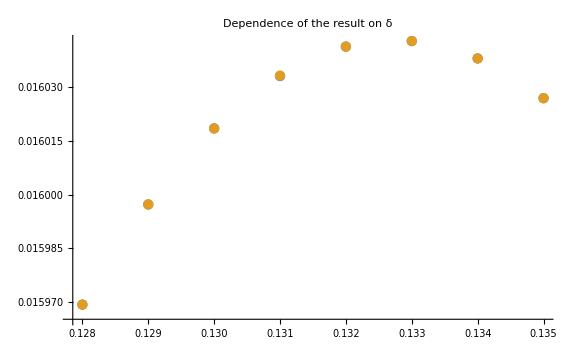

```mathematica
ListPlot[{Table[{fit[[j]][[1]],res[[j]]},{j,8}],Table[{fit[[j]][[1]],res[[j]]},{j,9,16}]},ImageSize->Large,PlotLabel->"Dependence of the result on δ"]
```

Good, so we can concentrate on .

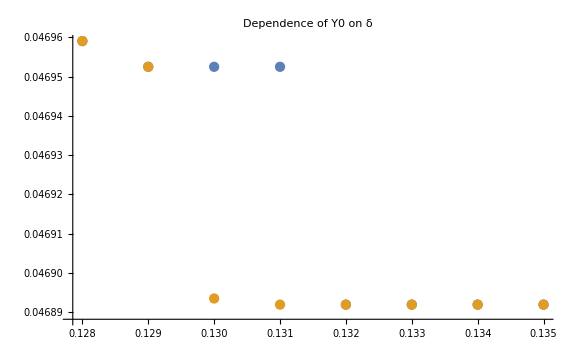

```mathematica
ListPlot[{Table[{fit[[j]][[1]],fit[[j]][[2]]},{j,8}],Table[{fit[[j]][[1]],fit[[j]][[2]]},{j,9,16}]},ImageSize->Large,PlotLabel->"Dependence of Y0 on δ",PlotRange->Full]
```

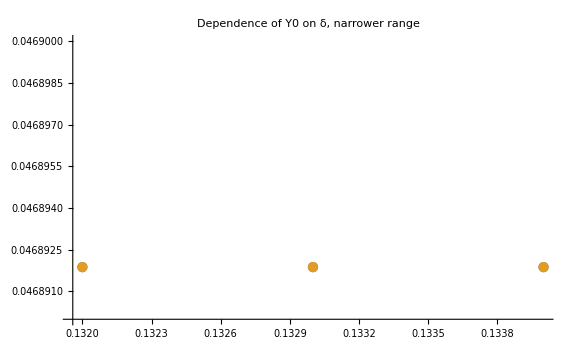

```mathematica
ListPlot[{Table[{fit[[j]][[1]],fit[[j]][[2]]},{j,5,7}],Table[{fit[[j]][[1]],fit[[j]][[2]]},{j,13,15}]},ImageSize->Large,PlotRange->{0.04689,0.0469},PlotLabel->"Dependence of Y0 on δ, narrower range"]
```

We can just take .

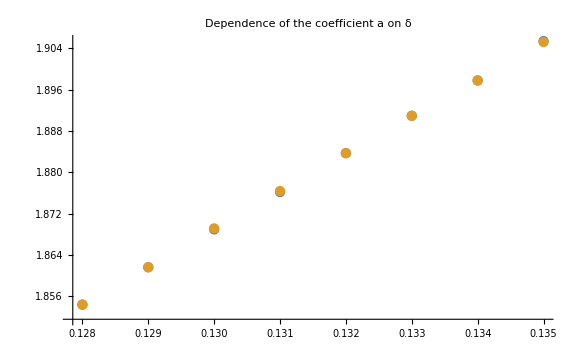

```mathematica
ListPlot[{Table[{fit[[j]][[1]],fit[[j]][[3]]},{j,8}],Table[{fit[[j]][[1]],fit[[j]][[3]]},{j,9,16}]},ImageSize->Large,PlotLabel->"Dependence of the coefficient a on δ"]
```

```mathematica
Fit[Table[{fit[[j]][[1]],fit[[j]][[3]]},{j,5,7}], {1,x,x^2}, x]
```

-2.49912+58.9844 x-195.313 x^2

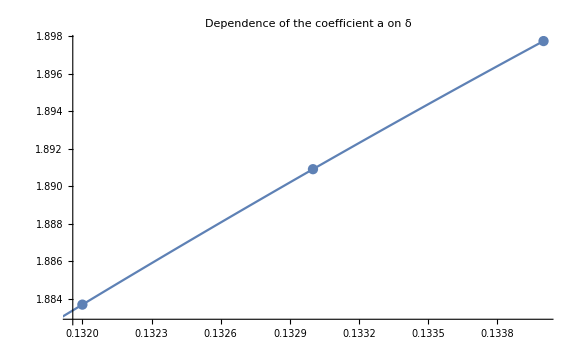

```mathematica
Show[{ListPlot[Table[{fit[[j]][[1]],fit[[j]][[3]]},{j,5,7}],ImageSize->Large,PlotLabel->"Dependence of the coefficient a on δ"],Plot[-2.4991210937616275+58.984375000174424 x-195.31250000065387 x^2,{x,0.131,0.134}]}]
```

```mathematica
Fit[Table[{fit[[j]][[1]],fit[[j]][[3]]},{j,13,15}], {1,x,x^2}, x]
```

-2.49912+58.9844 x-195.313 x^2

```mathematica
Show[{ListPlot[Table[{fit[[j]][[1]],fit[[j]][[3]]},{j,13,15}],ImageSize->Large,PlotLabel->"Dependence of the coefficient a on δ"],Plot[-2.4991210937582196+58.98437500012334 x-195.3125000004628 x^2,{x,0.131,0.134}]}]
```

-Graphics-

The second fit looks slightly better near 0.133.

```mathematica
resultFitted[delta_]:=resultApproximate[delta,0.14,0.046892,Interpolation[{{0,0},{1,-2.4991210937582196+58.98437500012334 delta-195.3125000004628 delta^2},{3,N[Pi,precision]},{4,N[Pi,precision]}},InterpolationOrder->1],1000,4000];
```

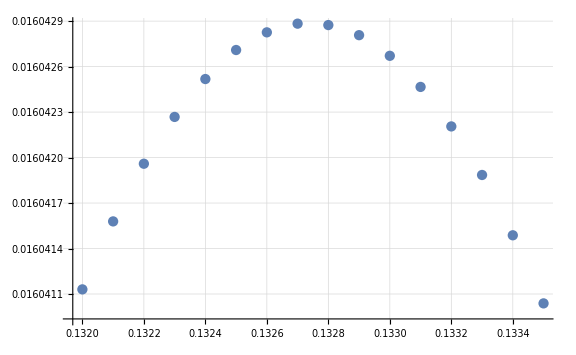

```mathematica
Parallelize[res=Table[{delta,resultFitted[delta]},{delta,0.132,0.1335001,0.0001}]];
listplot[res]
```

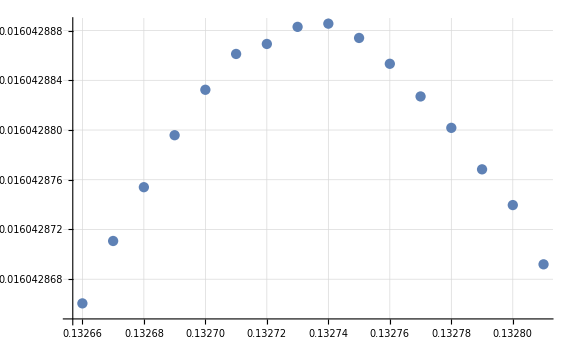

```mathematica
Parallelize[res=Table[{delta,resultFitted[delta]},{delta,0.13266,0.13281001,0.00001}]];
listplot[res]
```

```mathematica
delta=0.132737;
y0Fixed=0.046892;
aFixed=-2.4991210937582196+58.98437500012334 delta-195.3125000004628 delta^2;
resultApproximate[delta,0.14,y0Fixed,Interpolation[{{0,0},{1,aFixed},{3,N[Pi,precision]},{4,N[Pi,precision]}},InterpolationOrder->1],1000,4000]
```

0.01604288879728413441198883773201645654470961705251735108170976225437928281492206325821933233875859128

#### Re-fitting the basic parameters

Should we still change any of the parameters just a little?

```mathematica
Module[
{cRes=1000,wRes=4000},
y0Fixed=findMax[Function[y0,resultApproximate[delta,0.14,y0,Interpolation[{{0,0},{1,aFixed},{3,N[Pi,precision]},{4,N[Pi,precision]}},InterpolationOrder->1],cRes,wRes]],y0Fixed-0.0000016,y0Fixed+0.0000016,6][[1]];
aFixed=findMax[Function[a,resultApproximate[delta,0.14,y0Fixed,Interpolation[{{0,0},{1,a},{3,N[Pi,precision]},{4,N[Pi,precision]}},InterpolationOrder->1],cRes,wRes]],aFixed-0.002,aFixed+0.002,6][[1]];
y0Fixed=findMax[Function[y0,resultApproximate[delta,0.14,y0,Interpolation[{{0,0},{1,aFixed},{3,N[Pi,precision]},{4,N[Pi,precision]}},InterpolationOrder->1],cRes,wRes]],y0Fixed-0.0000016,y0Fixed+0.0000016,6][[1]];
aFixed=findMax[Function[a,resultApproximate[delta,0.14,y0Fixed,Interpolation[{{0,0},{1,a},{3,N[Pi,precision]},{4,N[Pi,precision]}},InterpolationOrder->1],cRes,wRes]],aFixed-0.002,aFixed+0.002,6][[1]];
];
```

```mathematica
resultApproximate[delta,0.14,y0Fixed,Interpolation[{{0,0},{1,aFixed},{3,N[Pi,precision]},{4,N[Pi,precision]}},InterpolationOrder->1],1000,4000]
```

0.01604289158889246906405381835627723436628448150333709647699165060473573821697789960999239449095721693

It seems we have the initial parameters. For the record, let us display their values...

```mathematica
y0Fixed
```

0.0468918

```mathematica
aFixed
```

1.8889

...and set them again to the same (useful if we had to close Mathematica and resume calculations later).

```mathematica
delta=0.132737;
y0Fixed=0.0468917625;
aFixed=1.888899;
```

## Fine-tuning the argument function

Now we try to fit an optimal piecewise-linear function to serve as the argument function for the contour we have selected. Of course, it is entirely possible that some other contour with a different argument function would give a better result, but we have no way to check that. We keep adding breakpoints to our piecewise linear function and find optimal values at each breakpoint individually, assuming that the other values remain unchanged. Then we compare results for argument functions of the form , where  is the new function,  the old function and . We pick the best one. We graph the argument functions labelling breakpoints with + or – if the argument function is convex, respectively concave at a given point. Gridlines correspond to divisions between horizontal and vertical parts of the right-hand side of the contour.

```mathematica
optimizeArguments[delta_,contourTop_,contourBottom_,argArr_,contourRes_,weightRes_,mobility_,iter_]:=Module[
{improvements,diffs,subst,m,res,top},
m=Length[argArr]-2;
subst[x_,j_]:=Join[argArr[[1;;j]],{{argArr[[j+1]][[1]],x}},argArr[[j+2;;m+2]]];
diffs=Table[argArr[[j+1]][[2]]-argArr[[j]][[2]],{j,m+1}];
Parallelize[improvements=Table[{argArr[[j+1]][[1]],findMax[Function[x,resultApproximate[delta,contourTop,contourBottom,Interpolation[subst[x,j],InterpolationOrder->1],contourRes,weightRes]],argArr[[j+1]][[2]]-mobility*diffs[[j]],argArr[[j+1]][[2]]+mobility*diffs[[j+1]],iter][[1]]},{j,m}]];
improvements=Join[{argArr[[1]]},improvements,{argArr[[m+2]]}];
Parallelize[res=Table[resultApproximate[delta,contourTop,contourBottom,Interpolation[(1-t)*argArr+t*improvements,InterpolationOrder->1],contourRes,weightRes],{t,0,1.99,1.0/8}]];
top=Ordering[res,-1][[1]];
Print[SetPrecision[res[[1]],8]," -> ",SetPrecision[res[[top]],8]," (moved by ",top-1,"/8)."];
(1-(top-1)/8)*argArr+((top-1)/8)*improvements
];
addBreakpoints[argArr_,points_]:=Module[{f,narr},
f=Interpolation[argArr,InterpolationOrder->1];
narr=Join[argArr,Table[{points[[j]],f[points[[j]]]},{j,1,Length[points]}]];
Sort[narr]
];
double[argArr_]:=addBreakpoints[argArr,Table[(argArr[[j]][[1]]+argArr[[j+1]][[1]])*0.5,{j,Length[argArr]-2}]];
show[argArr_]:=Module[{f,slope,signed},
f=Interpolation[argArr,InterpolationOrder->1];
slope[v_]:=v[[2]]/v[[1]];
signed[point_,change_]:=If[Abs[change]<10^(-6),point,
Labeled[point,If[change>0,"+","-"]]
];
Show[{Plot[f[x],{x,0,4},ImageSize->Large,GridLines->{{1,3},{f[1],f[3]}}],ListPlot[Table[signed[argArr[[j+1]],slope[argArr[[j+2]]-argArr[[j+1]]]-slope[argArr[[j+1]]-argArr[[j]]]],{j,Length[argArr]-2}]]},ImageSize->Full]
];
argArr={{0,0},{1,aFixed},{3,N[Pi,precision]},{4,N[Pi,precision]}};
```

0.016042892 -> 0.016382128 (moved by 8/8).

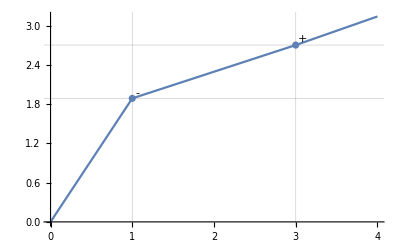

```mathematica
argArr=optimizeArguments[delta,0.14,y0Fixed,argArr,1000,4000,0.1,6];
show[argArr]
```

```mathematica
argArr
```

{{0,0},{1,1.889},{3,2.70413},{4,3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068}}

0.016382128 -> 0.016494354 (moved by 6/8).

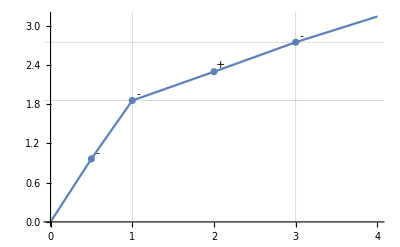

```mathematica
argArr=double[argArr];
argArr=optimizeArguments[delta,0.14,y0Fixed,argArr,1000,4000,0.1,6];
show[argArr]
```

```mathematica
argArr
```

{{0,0},{0.5,0.964974},{1,1.85579},{2.,2.29656},{3,2.74758},{4,3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068}}

0.016494354 -> 0.016553223 (moved by 5/8).

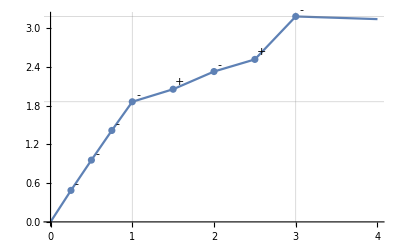

```mathematica
argArr=double[argArr];
argArr=optimizeArguments[delta,0.14,y0Fixed,argArr,1000,4000,0.1,6];
show[argArr]
```

```mathematica
argArr
```

{{0,0},{0.25,0.488141},{0.5,0.957472},{0.75,1.41669},{1,1.86111},{1.5,2.05541},{2.,2.32971},{2.5,2.51734},{3,3.18285},{4,3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068}}

0.016553223 -> 0.016555796 (moved by 8/8).

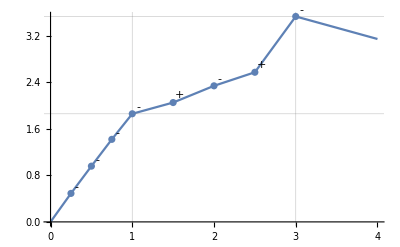

```mathematica
argArr=optimizeArguments[delta,0.14,y0Fixed,argArr,1000,4000,0.05,6];
show[argArr]
```

```mathematica
argArr
```

{{0,0},{0.25,0.489354},{0.5,0.957582},{0.75,1.41791},{1,1.8571},{1.5,2.04999},{2.,2.3371},{2.5,2.57011},{3,3.52876},{4,3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068}}

How far can we reach using a slightly higher resolution?

```mathematica
resultApproximate[delta,0.14,y0Fixed,Interpolation[argArr,InterpolationOrder->1],2000,20000]
```

0.01679563382490573709488766327227215050568532146353442110993364916712981506520709102199391581748152511

#### Are any of the breakpoints redundant?

If we include them in the paper, we should definitely make sure that each one is significant.

```mathematica
Parallelize[redundancyCheck=Table[resultApproximate[delta,0.14,y0Fixed,Interpolation[Join[argArr[[1;;j]],argArr[[j+2;;10]]],InterpolationOrder->1],2000,20000],{j,8}]];
```

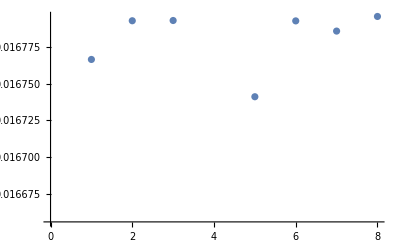

```mathematica
ListPlot[redundancyCheck]
```

```mathematica
Grid[{redundancyCheck}]
```

0.0167664042720772941227139352867723035522972136293616874356571791205910359234528583622950823222087487 | 0.0167927134047017459517646487265700815562344581136443311454616310643477165933042735150766861709090261 | 0.01679288383288203636877392462811443930025676019188017090167809491138197493093960407276569500594092738 | 0.01525966730161666488806523692395908083316797523737994021609503242342863374822767378433362641949613415 | 0.0167410557257297451739924166203893533129299225037512208151100872289914492533929274415271862767709073 | 0.01679262484030645488793851215836594897797589359985274756962866518958845127940478239459695851517013618 | 0.01678569299726448061757928428248101436681695039112929630016361789317909388872748087394621576949459193 | 0.01679563390648982876344509918811630063717497264179539001754720577254937109401046358039694367958591395

```mathematica
resultApproximate[delta,0.14,y0Fixed,Interpolation[Join[argArr[[1;;2]],argArr[[5;;6]],argArr[[8;;8]],argArr[[10;;10]]],InterpolationOrder->1],2000,20000]
```

0.01677126004139469194559618015201194319110500373476663157536497245859254128133679035026877854045607191

```mathematica
Join[argArr[[1;;2]],argArr[[5;;6]],argArr[[8;;8]],argArr[[10;;10]]]
```

{{0,0},{0.25,0.489354},{1,1.8571},{1.5,2.04999},{2.5,2.57011},{4,3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068}}

Since 3 is a natural breakpoint, we replace 2.5 with 3 and extrapolate the value so that the value at 2.5 will match.

```mathematica
Interpolation[Join[argArr[[1;;2]],argArr[[5;;6]],{{3,2.8301675617329556}},argArr[[10;;10]]],InterpolationOrder->1][2.5]
```

2.57011

```mathematica
resultApproximate[delta,0.14,y0Fixed,Interpolation[Join[argArr[[1;;2]],argArr[[5;;6]],{{3,2.8301675617329556}},argArr[[10;;10]]],InterpolationOrder->1],2000,20000]
```

0.01677126004139469194559618015201194319110500373476663157536497245859254128133679035026877854045607191

```mathematica
argArr=Join[argArr[[1;;2]],argArr[[5;;6]],{{3,2.8301675617329556}},argArr[[10;;10]]]
```

{{0,0},{0.25,0.489354},{1,1.8571},{1.5,2.04999},{3,2.83017},{4,3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068}}

0.016531535 -> 0.016534666 (moved by 8/8).

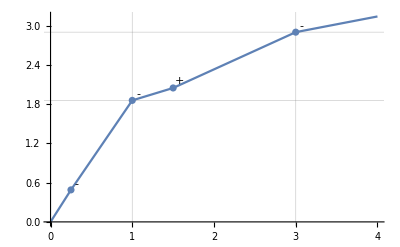

{{0,0},{0.25,0.489748},{1,1.8581},{1.5,2.04819},{3,2.90139},{4,3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068}}

```mathematica
argArr=optimizeArguments[delta,0.14,y0Fixed,argArr,1000,4000,0.1,6];
show[argArr]
argArr
```

0.016534666 -> 0.016534671 (moved by 3/8).

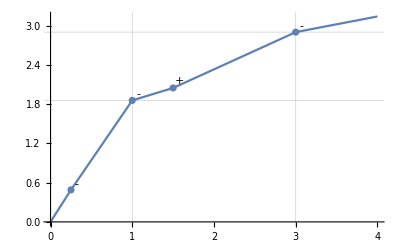

{{0,0},{0.25,0.489819},{1,1.85801},{1.5,2.04829},{3,2.90189},{4,3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068}}

```mathematica
argArr=optimizeArguments[delta,0.14,y0Fixed,argArr,1000,4000,0.05,6];
show[argArr]
argArr
```

```mathematica
resultApproximate[delta,0.14,y0Fixed,Interpolation[argArr,InterpolationOrder->1],2000,20000]
```

0.01677441371106705930111151922660709059040228404179804150851620685114102749277699402331861851776791578

```mathematica
{delta,0.14,y0Fixed,argArr}
```

{0.132737,0.14,0.0468918,{{0,0},{0.25,0.489819},{1,1.85801},{1.5,2.04829},{3,2.90189},{4,3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068}}}

## A semi-rigorous estimate of the final result

Now we compute the final result, taking into account not only the values of cFNEta[] at selected contour points, but also its changes in-between. This is basically the final value mentioned in the paper, but it cannot be considered quite rigorous, as we do not use interval arithmetic here.

```mathematica
result[(* contour position *) paramdelta_?NumericQ,paramcontourTop_?NumericQ,paramcontourBottom_?NumericQ,(* a function that goes from the value 0 at 0 to the value π at 4, that determines α_j`s in the paper *) argFun_,
(* half of the number of divisions of the contour on each side *) contourRes_?NumericQ,
(* the resolution for approximating weight functions *) weightRes_?IntegerQ
]:=
Module[
{
delta,contourTop,contourBottom,
m,t,z1,cRNArray,alpha,
b,xPrime,xBis,y,
indexForRN,M,u,
betaPrime,betaBis,phiPrime,phiBis,c,symmetricPairs,phi,c0j,cn0,
operation,wnInverse,wnMax,localc,localphi,cosphi,iMax,cosValue,previous,product,volume,returnValue,
epsmachine,
i,j,n
},
delta=SetPrecision[paramdelta,precision];
contourTop=SetPrecision[paramcontourTop,precision];
contourBottom=SetPrecision[paramcontourBottom,precision];
m=8*contourRes;
t[j_]:=j/m;
(* z1(t_j) is to be stored as z1[[j+1]]. *)
z1=Join[
Table[(-0.5`100+j/(2*contourRes))*delta+contourBottom*I,{j,0,2*contourRes}],
Table[0.5`100*delta+(contourBottom+(contourTop-contourBottom)*j/(2*contourRes))*I,{j,1,2*contourRes}],
Table[(0.5`100-j/(2*contourRes))*delta+contourTop*I,{j,1,2*contourRes}],
Table[-0.5`100*delta+(contourTop-(contourTop-contourBottom)*j/(2*contourRes))*I,{j,1,2*contourRes}]
];
(*Monitor[*)cRNArray=Table[cRNest[(contourBottom+(contourTop-contourBottom)*j/(2*contourRes))],{j,0,2*contourRes}](*,StringJoin["Computing the estimate for R_N(s) along the contour: ",ToString[j+1]," of ",ToString[2*contourRes+1]," points."]]*);
(* We define and compute further quantities in the order in which they appear in the section "The proof of Theorem 1" of the paper. *)

 (* α_1,...,α_{m+1} *)
alpha=Join[Table[-Pi-argFun[1-(j-0.5`100)/contourRes],{j,1,contourRes}],
Table[-Pi+argFun[(j-0.5`100)/contourRes],{j,1,4*contourRes}],
Table[Pi-argFun[4-(j-0.5`100)/contourRes],{j,1,3*contourRes+1}]];

(*Claim 1.*)
(*Subsequent alpha[[j]] should differ by less than π.*)
If[Max[Table[Abs[alpha[[j+1]]-alpha[[j]]],{j,1,m}]]>Pi-error,
Return[-1.1]];
(*This value should be less than π.*)
If[Max[Table[Abs[z1[[j+1]]-z1[[j]]],{j,1,m}]]*omega[cN]>Pi-error,
Return[-1.2]];

b=Table[Abs[z1[[j]]-z1[[j+1]]]/2,{j,1,m}];
xPrime=Table[Min[Re[z1[[j]]],Re[z1[[j+1]]]],{j,1,m}];
xBis=Table[Max[Re[z1[[j]]],Re[z1[[j+1]]]],{j,1,m}];
y=Table[Min[Im[z1[[j]]],Im[z1[[j+1]]]],{j,1,m}];
indexForRN=Join[
Table[1,{j,1,2*contourRes}],
Table[j,{j,1,2*contourRes}],
Table[2*contourRes+1,{j,1,2*contourRes}],
Table[2*contourRes+1-j,{j,1,2*contourRes}]
]; 
(* We have cRN[y[[j]]]==cRNArray[[indexForRN[[j]]]] *)
(* Print["Discrepancy for RN: ",Max[Table[Abs[cRNprec[y[[j]]]-cRNArray[[indexForRN[[j]]]]],{j,1,m}]]];*)
M=Table[error+Sum[aUpperBound[n]*omega[n]^2*Exp[-omega[n]*y[[j]]],{n,1,cN}],{j,1,m}];
u=Table[
Min[
Re[cFNEta[z1[[j]]]Exp[-I*alpha[[j]]]]+Min[0,Re[b[[j]]*f[z1[[j]]]Exp[-I*alpha[[j]]]]],
Re[cFNEta[z1[[j+1]]]Exp[-I*alpha[[j]]]]+Min[0,-Re[b[[j]]*f[z1[[j+1]]]Exp[-I*alpha[[j]]]]]
]-b[[j]]*b[[j]]*M[[j]]/2-cRNArray[[indexForRN[[j]]]],
{j,1,m}
];

(*Claim 2.*)
(*This value should be positive.*)
If[Min[u]<error,
Return[-2]];

betaPrime=Table[Table[
Pi+omega[n]*xPrime[[j]]-alpha[[j]],
{j,1,m}],{n,1,cN}];
betaBis=Table[Table[
Pi+omega[n]*xBis[[j]]-alpha[[j]],
{j,1,m}],{n,1,cN}];

(*Claim 3.*)
(*The differences betaBis[[n]][[j]]-betaPrime[[n]][[j]] should be less than π.*)
If[Max[Table[Table[
betaBis[[n]][[j]]-betaPrime[[n]][[j]],
{j,1,m}],{n,1,cN}]]>Pi-error,
Return[-3]];

phiPrime=Table[Table[
If[Ceiling[betaPrime[[n]][[j]]/(2*Pi)]<=Floor[betaBis[[n]][[j]]/(2*Pi)],
0,
2*Pi*Min[norm[betaPrime[[n]][[j]]/(2*Pi)],norm[betaBis[[n]][[j]]/(2*Pi)]]
],
{j,1,m}],{n,1,cN}];
phiBis=Table[Table[
If[Ceiling[(betaPrime[[n]][[j]]+Pi)/(2*Pi)]<=Floor[(betaBis[[n]][[j]]+Pi)/(2*Pi)],
Pi,
2*Pi*Max[norm[betaPrime[[n]][[j]]/(2*Pi)],norm[betaBis[[n]][[j]]/(2*Pi)]]
],
{j,1,m}],{n,1,cN}];
c=Table[Table[
(aUpperBound[n]/u[[j]])*Exp[-omega[n]*y[[j]]]*
Which[
phiBis[[n]][[j]]<=Pi/2,1/Cos[(phiBis[[n]][[j]]-phiPrime[[n]][[j]])/2],
phiPrime[[n]][[j]]>=Pi/2,1,
True,1/Cos[(Pi/2-phiPrime[[n]][[j]])/2]
],
{j,1,m}],{n,1,cN}];
(* 
Because of the symmetry cFNEta[-x+y I]==cFNEta[x+y I] we can skip half of the intervals.
This part does not appear in the paper as it is just a numerical optimization.
We do not include it in the rigorous check.
This allows us to shorten the iterative process of choosing best division points.
*)
symmetricPairs=Join[Range[contourRes,1,-1],Range[m,5*contourRes+1,-1]];
If[Max[Max[Table[Table[Abs[c[[n]][[j]]-c[[n]][[symmetricPairs[[j-contourRes]]]]],{j,contourRes+1,5*contourRes}],{n,1,cN}]],
Max[Table[Table[Abs[phiPrime[[n]][[j]]-phiPrime[[n]][[symmetricPairs[[j-contourRes]]]]],{j,contourRes+1,5*contourRes}],{n,1,cN}]],
Max[Table[Table[Abs[phiBis[[n]][[j]]-phiBis[[n]][[symmetricPairs[[j-contourRes]]]]],{j,contourRes+1,5*contourRes}],{n,1,cN}]]]>error,
Return[-0.5]
];

(* We leave out the repeated entries. *)
For[n=1,n<=cN,n++,
c[[n]]=c[[n]][[contourRes+1;;5*contourRes]];
phiPrime[[n]]=phiPrime[[n]][[contourRes+1;;5*contourRes]];
phiBis[[n]]=phiBis[[n]][[contourRes+1;;5*contourRes]];
];
u=u[[contourRes+1;;5*contourRes]];
y=y[[contourRes+1;;5*contourRes]];

(* We will be evaluating , so we merge phiPrime and phiBis to make it simpler. *)
phi=Table[Join[phiPrime[[n]],phiBis[[n]]],{n,1,cN}];
For[n=1,n<=cN,n++,
c0j=Select[Range[m/2],Function[j,phiBis[[n]][[j]]>=Pi/2&&phiPrime[[n]][[j]]<=Pi/2]];(* The set of j for  *)
If[Length[c0j]==0,
(* The restricted max was empty, no need to add . *)
c[[n]]=Join[c[[n]],c[[n]]]
,
(* We do need to add  and . *)
cn0=aUpperBound[n]*Max[Table[Exp[-omega[n]*y[[c0j[[i]]]]]/(u[[c0j[[i]]]]*Cos[(Pi/2-phiPrime[[n]][[c0j[[i]]]])/2]),{i,1,Length[c0j]}]];
c[[n]]=Join[c[[n]],c[[n]],{cn0}];
phi[[n]]=Join[phi[[n]],{Pi/2}]
]
];
wnMax=Table[Min[1,Max[Table[(c[[n]][[j]]+error)*(Cos[phi[[n]][[j]]]+1),{j,Length[c[[n]]]}]]],{n,cN}];
For[n=cN-1,n>=1,n--,wnMax[[n]]+=wnMax[[n+1]]];
For[n=cN,n>=1,n--,
operation="Computing";
epsmachine=0.0+epsilon;
wnInverse=Table[0.5,{i,weightRes}];
For[j=1,j<=Length[c[[n]]],j++,
localc=0.0+c[[n]][[j]]+error;(*To machine precision*)
localphi=0.0+phi[[n]][[j]];
cosphi=Cos[localphi];
iMax=Floor[Min[1,localc*(cosphi+1)]*weightRes];
For[i=1,i<=iMax,i++,
(*Solve c(Cos[ϕ]-Cos[ϕ+2π(epsilon+x)])==i/weightRes*)
cosValue=cosphi-i/(weightRes*localc);
wnInverse[[i]]=Min[wnInverse[[i]],(ArcCos[cosValue]-localphi)/(2 Pi)-epsmachine]
];
];
For[i=weightRes,i>=1,i--,
wnInverse[[i]]=Floor[wnInverse[[i]]*weightRes^2]
];
For[i=weightRes,i>=2,i--,
wnInverse[[i]]-=wnInverse[[i-1]]
];
If[n==cN,
previous=wnInverse
,
operation="Convoluting";
product=Join[{0},ListConvolve[previous,wnInverse,1,0][[1;;weightRes-1]]];
previous=product
]
];
volume=2^cN*Sum[product[[i]],{i,weightRes}]/weightRes^(2 cN);
returnValue=2*volume/delta;
returnValue
];
```

```mathematica
result[0.132737,0.14,0.0468917625,Interpolation[{{0,0},{0.25`100,0.48981938638676636`100},{1,1.858014753262597`100},{1.5`100,2.048292798102907`100},{3,2.9018918260604507`100},{4,Pi}},InterpolationOrder->1],1000,4000]
```

0.01635385960589345930692005278570505594408064710831537827956666067749797505863752833728283430096530325

Maybe we do not need that many digits.

```mathematica
result[0.132737,0.14,0.0468918,Interpolation[{{0,0},{0.25`100,0.489819`100},{1,1.85802`100},{1.5`100,2.04829`100},{3,2.90189`100},{4,Pi}},InterpolationOrder->1],1000,4000]
```

0.01635387324557644992522443690447618120055556263774533553796306188674195100368282344566890221241259971

What resolution do we actually need?

```mathematica
result[0.132737,0.14,0.0468918,Interpolation[{{0,0},{0.25`100,0.489819`100},{1,1.85802`100},{1.5`100,2.04829`100},{3,2.90189`100},{4,Pi}},InterpolationOrder->1],2500,10000]
```

0.01664083784842868217940084948617604685742928015712789706041265373402373952522986361865837050791093657

```mathematica
result[0.132737,0.14,0.0468918,Interpolation[{{0,0},{0.25`100,0.489819`100},{1,1.85802`100},{1.5`100,2.04829`100},{3,2.90189`100},{4,Pi}},InterpolationOrder->1],1500,16000]
```

0.01667574149646089128633650564032035367233254994345336437476441510484664952584251549384941220928175622

It seems that the resolutions 1500/16000 will be perfectly sufficient to obtain 1/60 as the final result, and we could not get a significantly greater result by increasing the resolution.

Finally, we note that in the paper the entire contour is defined on [0,1], whereas the argument function above was on [0,4] for just one half of the contour. Therefore the argument function α(t) in the paper has appropriately rescaled breakpoints.